## Метод Чебышева 2.1.8

#### Подготовил Ерофеевский Александр ПМ-1801

Дано: функция f(x), начальное приближение x0, количество итераций k

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
ClearAll@chebyshevsMethod
chebyshevsMethod[f_,x0_,k_]:=Module[
{x = x0},
Do[
x = x -  f[x]/ND[f[s],s,x]- (f[x]^2*ND[f[s],{s,2},x])/(2*(ND[f[s],s,x])^3),
{i,1,k}];
x]
```

Результаты

Пример 1

```mathematica
Clear@f
f[x_]:=x^3-4 x^2+10x-10
x0 = 1;
k = 10;
```

```mathematica
chebyshevsMethod[f,x0,k]
```

1.62936

Проверка

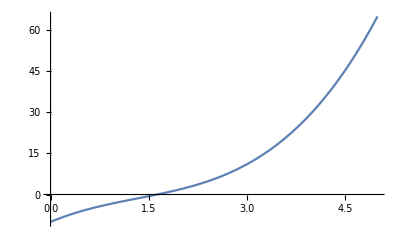

```mathematica
Plot[f[x],{x,0,5}]
```

```mathematica
N[Solve[f[x]==0]]
```

{{x→1.62936},{x→1.18532+2.17541 ⅈ},{x→1.18532-2.17541 ⅈ}}

Пример 2

```mathematica
Clear@f
f[x_]:=x^3+6 x^2+9x-4
x0 = 1;
k = 10;
```

```mathematica
chebyshevsMethod[f,x0,k]
```

0.355301

Проверка

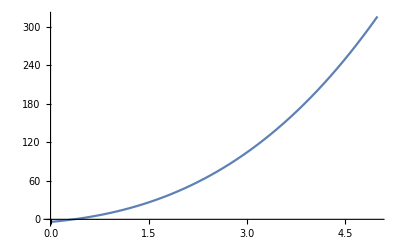

```mathematica
Plot[f[x],{x,0,5}]
```

```mathematica
N[Solve[f[x]==0]]
```

{{x→0.355301},{x→-3.17765+1.0773 ⅈ},{x→-3.17765-1.0773 ⅈ}}